# Text Learning

```mathematica
labels={"AliceInWonderland","BeowulfModern","DonQuixoteIEnglish","Hamlet","OriginOfSpecies"};
```

```mathematica
texts=Map[{"Text",#}&,labels];
```

```mathematica
rawdata=RandomSample[
Flatten[
Map[
Function[{text},
Map[#->Last[text]&,
RandomSample[TextSentences[DeleteStopwords@ExampleData[text]],400]
]],
texts
]]];
```

```mathematica
dictionary=Select[Union[Flatten[Map[TextWords[First[#]]&,rawdata]]],DictionaryLookup[#]=!={}&];
```

```mathematica
Length[dictionary]
```

6394

```mathematica
TextEncoder[string_]:=Module[{vector,positions},
vector=ConstantArray[0,Length[dictionary]];
positions=Flatten[Position[dictionary,#]&/@Select[TextWords[string],DictionaryLookup[#]=!={}&]];
vector[[positions]]=1;
vector
]
```

```mathematica
data=Map[TextEncoder[First[#]]->Last[#]&,rawdata];
```

```mathematica
Length[data]
```

2000

```mathematica
training=data[[;;1800]];
validation=data[[1801;;]];
```

```mathematica
net=NetChain[{1000,Ramp,5,Ramp,SoftmaxLayer[]},"Input"->Length[dictionary],"Output"->NetDecoder[{"Class",labels}]]
```

NetChain[]

```mathematica
net=NetInitialize[net];
```

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
net=NetInitialize[net];
net=NetTrain[net,training,ValidationSet->validation,TargetDevice->"GPU"]
```

NetChain[]

#### Check it

```mathematica
cm=ClassifierMeasurements[net,validation];
```

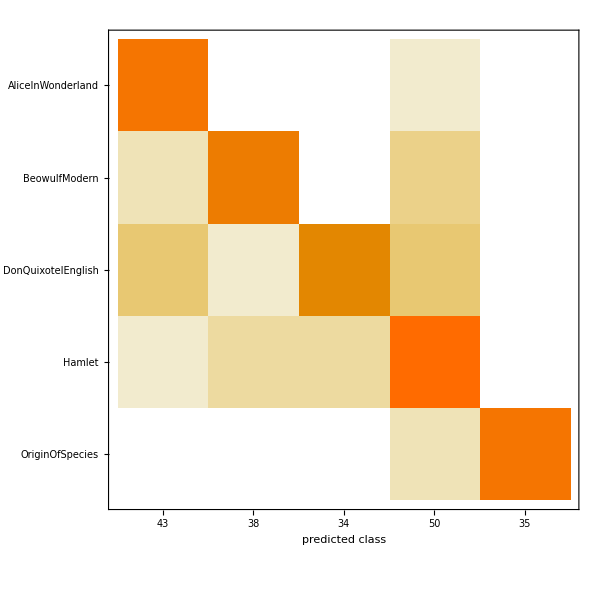

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

0.865

```mathematica
Grid[Reverse/@(RandomSample[rawdata,40]/.{Rule->List}),Frame->All]
```

BeowulfModern | came   mind  bid  henchmen  hall uprear,  master mead-house, mightier far    seen   sons  earth,   , ,  old  young    allot   Lord  sent , save   land   lives   men.
Hamlet | [Enter Hamlet, Horatio,  Marcellus.] Ham.
AliceInWonderland | "  tarts  ?" "Pepper, ," said  cook.
AliceInWonderland | Just  Alice ran   Duchess (     prison).
BeowulfModern | 'Twas granted      edge  iron    help   strife:  strong   hand,   tale  told,   tried  far  strength  stroke  swords  wielded,  sturdy  steel:  steaded  nought.
OriginOfSpecies | Recapitulation   difficulties   theory  Natural Selection.
BeowulfModern | Lo, sudden  shift!
OriginOfSpecies | masters determine     new nest shall  formed,    migrate,  masters carry  slaves.
OriginOfSpecies | , , reason  suspect,  information given   Mr. W. W. Edwards,    English race-horse  spinal stripe   commoner   foal    -grown animal.
OriginOfSpecies | nature variability   powerful agent  ready  act  select,    doubt  variations   way useful  beings,   excessively complex relations  life,   preserved, accumulated,  inherited?
BeowulfModern | death  yore  hurried  hence;    left  live,     clan, weeping  friends,  wished  bide warding  treasure,   delight,  brief  respite.
AliceInWonderland | considering    mind (    ,   day   feel  sleepy  stupid),   pleasure  making  daisy-chain   worth  trouble  getting   picking  daisies,  suddenly  White Rabbit  pink eyes ran close  .
DonQuixoteIEnglish | Anselmo,   true,  somewhat  inclined  seek pleasure  love  Lothario,    pleasures   chase   attraction;   occasion Anselmo  forego   tastes  yield    Lothario,  Lothario  surrender   fall     Anselmo,    way  inclinations kept pace       concord  perfect   best regulated clock   surpass .
OriginOfSpecies | Certainly  clear line  demarcation     drawn  species  sub-species-- ,  forms    opinion   naturalists come  near ,    quite arrive   rank  species; , ,  sub-species  -marked varieties,   lesser varieties  individual differences.
DonQuixoteIEnglish | know   devil   come ,    love     got ;    young girl,     mere boy;   verily believe      age,     sixteen ;     sixteen Michaelmas Day, ,  father says."
DonQuixoteIEnglish | Anselmo   believe ,  blind  rage drew  dagger  threatened  stab Leonela, bidding  tell  truth    kill .
AliceInWonderland | invitation   Queen  play croquet."
OriginOfSpecies | stated    chapter,     evidence  render  probable,   whatever age  variation  appears   parent,  tends  reappear   corresponding age   offspring.
Hamlet | backed like  weasel.
DonQuixoteIEnglish | gone   miles Don Quixote perceived  large party  people, ,  afterwards appeared,   Toledo traders,   way  buy silk  Murcia.
OriginOfSpecies | Undoubtedly     important point  difference  varieties  species; namely,   amount  difference  varieties,  compared       parent-species,        species    genus.
AliceInWonderland | Alice said  ,       sneezing.
OriginOfSpecies | asserted,    best short-beaked tumbler-pigeons  perish   egg   able     ;   fanciers assist   act  hatching.
Hamlet | King.
DonQuixoteIEnglish | Bethink thee     seeks impossibilities    possible   justice  withheld,   better expressed   poet  said: 'Tis mine  seek  life  death, Health  disease seek ,  seek  prison freedom's breath,  traitors loyalty.
DonQuixoteIEnglish | care  pains  unavailing,   master   discovery      man,  harboured   base designs   servant;   fortune    supply  remedy  cases  difficulty,     precipice  ravine  hand    fling  master  cure  passion,      servant's case,  thought   lesser evil  leave    conceal    crags,  make trial   strength  argument  . ,   say,    went  hiding  seek   place     sighs  tears implore Heaven   pity   misery,  grant  help  strength  escape  ,  let  die   solitudes, leaving  trace   unhappy  ,   fault  ,  furnished matter  talk  scandal  home  abroad."
Hamlet | Laer.
Hamlet | loves  ;    soil  cautel doth besmirch  virtue   :    fear,  greatness weigh'd,      ;     subject   birth:   ,  unvalu'd persons , Carve  ;    choice depends  safety  health    state;     choice  circumscrib'd Unto  voice  yielding   body Whereof    head.
OriginOfSpecies | plants  animals migrated southward,     mingled    great region   native American productions,     compete  ;     great region,     Old World.
AliceInWonderland | just   taken  highest tree   wood," continued  Pigeon, raising  voice   shriek, " just    thinking    free    ,   needs come wriggling    sky!
AliceInWonderland | caused  remarkable sensation   party.
OriginOfSpecies | superfluous  remark  hardly  fossil-fish  known  south   equator;   running  Pictet's Palaeontology    seen    species  known   formations  Europe.
AliceInWonderland | IV-- RABBIT SENDS   LITTLE BILL    White Rabbit, trotting slowly    looking anxiously    went,     lost ; Alice heard  muttering  , " Duchess!
DonQuixoteIEnglish | " God's name, , senor," replied Don Quixote; "   ,     know    held enchanted   cage   envy  fraud  wicked enchanters;  virtue   persecuted   wicked  loved   good.
Hamlet | Queen.
BeowulfModern | song  glee.
OriginOfSpecies | feel assured    individuals    species,    closely allied species   genera,      remote period descended   parent,   migrated    birthplace;    better know   means  migration, ,   light  geology  throws,   continue  throw,  former changes  climate    level   land,  shall surely  enabled  trace   admirable manner  former migrations   inhabitants    world.
BeowulfModern | came   killed   sword nine   nicors.
AliceInWonderland | moment  felt  violent blow underneath  chin--  struck  foot!
BeowulfModern | kissed  king  kin renowned, Scyldings' chieftain,  choicest thane,  fell   neck.